```mathematica
ClearAll["Global`*"];

(* ==========EPSILONS==========*)

epsilons={0,0.25,0.5,0.75,0.9};

(* ==========ACOPLAMIENTOS==========*)

beta[eps_]:=(1-eps)/2;
betaprima[eps_]:=(1+eps)/2;

(* ==========BANDAS DE ENERGÍA==========*)

e[k_,eps_]:=Sqrt[beta[eps]^2+betaprima[eps]^2+2 beta[eps] betaprima[eps] Cos[k]];

Plot[Evaluate[Table[{e[k,eps],-e[k,eps]},{eps,epsilons}]],{k,-Pi,Pi},Frame->True,FrameLabel->{"k","E(k)"},PlotLabel->"Bandas de energía para diferentes ϵ",PlotLegends->Flatten[Table[{"ϵ = "<>ToString[eps],"ϵ = "<>ToString[eps]},{eps,epsilons}]],PlotRange->All,ImageSize->Large]
```

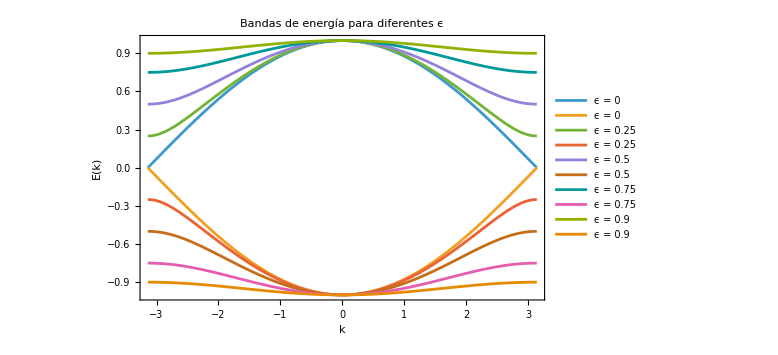

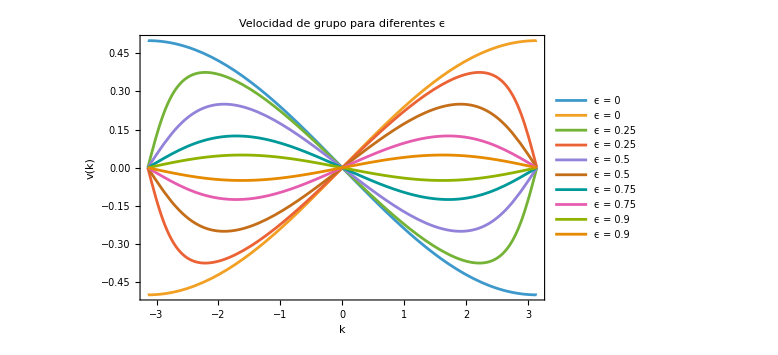

```mathematica
(* ==========VELOCIDAD DE GRUPO==========*)v[k_,eps_]:=-beta[eps] betaprima[eps] Sin[k]/e[k,eps];

Plot[Evaluate[Table[{v[k,eps],-v[k,eps]},{eps,epsilons}]],{k,-Pi,Pi},Frame->True,FrameLabel->{"k","v(k)"},PlotLabel->"Velocidad de grupo para diferentes ϵ",PlotLegends->Flatten[Table[{"ϵ = "<>ToString[eps],"ϵ = "<>ToString[eps]},{eps,epsilons}]],PlotRange->All,ImageSize->Large]
```

```mathematica
vmax[eps_]:=Min[beta[eps],betaprima[eps]];

Table[{eps,beta[eps],betaprima[eps],vmax[eps]},{eps,epsilons}]
```

{{0,1/2,1/2,1/2},{0.25,0.375,0.625,0.375},{0.5,0.25,0.75,0.25},{0.75,0.125,0.875,0.125},{0.9,0.05,0.95,0.05}}